```mathematica
SetDirectory[NotebookDirectory[]];
S0listneg=Import["S0listneg","list"];
A0listneg=Import["A0listneg","list"];
S1listneg=Import["S1listneg","list"];
A1listneg=Import["A1listneg","list"];
S2listneg=Import["S2listneg","list"];
A2listneg=Import["A2listneg","list"];
Eflistneg=Import["Eflistneg","list"];
indlistneg=Import["dlistneg","list"];
indeltalistneg=Import["deltalistneg","list"];

S0listpos=Import["S0listpos","list"];
A0listpos=Import["A0listpos","list"];
S1listpos=Import["S1listpos","list"];
A1listpos=Import["A1listpos","list"];
S2listpos=Import["S2listpos","list"];
A2listpos=Import["A2listpos","list"];
Eflistpos=Import["Eflistpos","list"];
indlistpos=Import["dlistpos","list"];
indeltalistpos=Import["deltalistpos","list"];


S0list=Import["S0list","list"];
A0list=Import["A0list","list"];
S1list=Import["S1list","list"];
A1list=Import["A1list","list"];
S2list=Import["S2list","list"];
A2list=Import["A2list","list"];
Eflist=Import["Eflist","list"];
indlist=Import["dlist","list"];
indeltalist=Import["deltalist","list"];
```

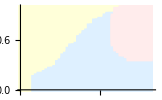

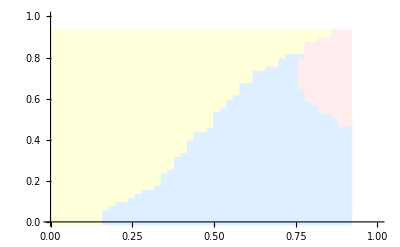

```mathematica
nS0list={};
nS1list={};
nA0list={};
nA1list={};
Apoints={};
Spoints={};
Cpoints={};

For[n=0,n<=Length[S0list],n=n+1,{
If[0.1<Abs[S0list[[n]]]<3,{nS0list=Append[nS0list,n]}],
If[0.1<Abs[S1list[[n]]]<3,nS1list=Append[nS1list,n]],
If[0.1<Abs[A0list[[n]]]<3,nA0list=Append[nA0list,n]],
If[0.1<Abs[A1list[[n]]]<3,nA1list=Append[nA1list,n]],
If[0.1<Abs[S1list[[n]]]<3,Apoints=Append[Apoints,{indeltalist[[n]],indlist[[n]]}]],
If[0.1<Abs[A1list[[n]]]<3 && 0.1>Abs[S1list[[n]]],Spoints=Append[Spoints,{indeltalist[[n]],indlist[[n]]}]],
If[0.1>Abs[A1list[[n]]]||Abs[A1list[[n]]]>3,Cpoints=Append[Cpoints,{indeltalist[[n]],indlist[[n]]}]]}];

plotc=ListPlot[Cpoints,PlotMarkers->{"■",27},PlotStyle->{LightYellow},PlotRange->{{0,1},{0,1}}];
plota=ListPlot[Apoints,PlotMarkers->{"■",27},PlotStyle->{LightPink},PlotRange->{{0,1},{0,1}}];
plots=ListPlot[Spoints,PlotMarkers->{"■",27},PlotStyle->{LightBlue},PlotRange->{{0,1},{0,1}}];
Print[Show[{plotc,plots,plota},BaseStyle->{FontSize->16}]]

plotc=ListPlot[Cpoints,PlotMarkers->{"■",15},PlotStyle->{LightYellow},PlotRange->{{0,1},{0,1}}];
plota=ListPlot[Apoints,PlotMarkers->{"■",15},PlotStyle->{LightPink},PlotRange->{{0,1},{0,1}}];
plots=ListPlot[Spoints,PlotMarkers->{"■",15},PlotStyle->{LightBlue},PlotRange->{{0,1},{0,1}}];
Print[Show[{plotc,plots,plota},BaseStyle->{FontSize->16}]]
```

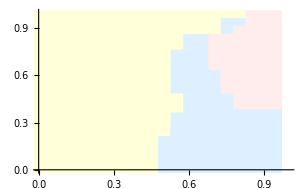

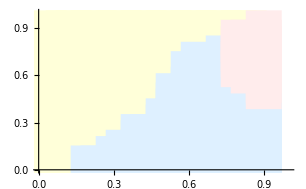

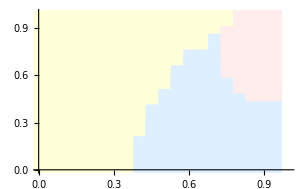

```mathematica
S0list=Import["S0list","list"];
A0list=Import["A0list","list"];
S1list=Import["S1list","list"];
A1list=Import["A1list","list"];
S2list=Import["S2list","list"];
A2list=Import["A2list","list"];
Eflist=Import["Eflist","list"];
indlist=Import["dlist","list"];
indeltalist=Import["deltalist","list"];

len=Length[indeltalist]/225;
For[n=1,n<=len,n=n+1,{i=225*n,
indeltalist=Drop[indeltalist,{-(2*n-1)*45,-((2*n-1)*45-44)}],
indlist=Drop[indlist,{-(2*n-1)*45,-((2*n-1)*45-44)}],
S0list=Drop[S0list,{-(2*n-1)*45,-((2*n-1)*45-44)}],
S1list=Drop[S1list,{-(2*n-1)*45,-((2*n-1)*45-44)}],
S2list=Drop[S2list,{-(2*n-1)*45,-((2*n-1)*45-44)}],
A0list=Drop[A0list,{-(2*n-1)*45,-((2*n-1)*45-44)}],
A1list=Drop[A1list,{-(2*n-1)*45,-((2*n-1)*45-44)}],
A2list=Drop[A2list,{-(2*n-1)*45,-((2*n-1)*45-44)}],
indeltalist=Drop[indeltalist,{-(2*n+1)*45,-((2*n+1)*45-44)}],
indlist=Drop[indlist,{-(2*n+1)*45,-((2*n+1)*45-89)}],
S0list=Drop[S0list,{-(2*n+1)*45,-((2*n+1)*45-89)}],
S1list=Drop[S1list,{-(2*n+1)*45,-((2*n+1)*45-89)}],
S2list=Drop[S2list,{-(2*n+1)*45,-((2*n+1)*45-89)}],
A0list=Drop[A0list,{-(2*n+1)*45,-((2*n+1)*45-89)}],
A1list=Drop[A1list,{-(2*n+1)*45,-((2*n+1)*45-89)}],
A2list=Drop[A2list,{-(2*n+1)*45,-((2*n+1)*45-89)}]}]

nS0listpos={};
nS1listpos={};
nA0listpos={};
nA1listpos={};
Apointspos={};
Spointspos={};
Cpointspos={};

For[n=0,n<=Length[S1listpos],n=n+1,{
If[0.1<Abs[S0listpos[[n]]]<3,{nS0listpos=Append[nS0listpos,n]}],
If[0.1<Abs[S1listpos[[n]]]<3,nS1listpos=Append[nS1listpos,n]],
If[0.1<Abs[A0listpos[[n]]]<3,nA0listpos=Append[nA0listpos,n]],
If[0.1<Abs[A1listpos[[n]]]<3,nA1listpos=Append[nA1listpos,n]],
If[0.1<Abs[S1listpos[[n]]]<3,Apointspos=Append[Apointspos,{indeltalistpos[[n]],indlistpos[[n]]}]],
If[0.1<Abs[A1listpos[[n]]]<3 && 0.1>Abs[S1listpos[[n]]],Spointspos=Append[Spointspos,{indeltalistpos[[n]],indlistpos[[n]]}]],
If[0.1>Abs[A1listpos[[n]]]||Abs[A1listpos[[n]]]>3,Cpointspos=Append[Cpointspos,{indeltalistpos[[n]],indlistpos[[n]]}]]}];

plotcp=ListPlot[Cpointspos,PlotMarkers->{"■",37},PlotStyle->{LightYellow},PlotRange->{{0,1},{0,1}}];
plotap=ListPlot[Apointspos,PlotMarkers->{"■",37},PlotStyle->{LightPink},PlotRange->{{0,1},{0,1}}];
plotsp=ListPlot[Spointspos,PlotMarkers->{"■",37},PlotStyle->{LightBlue},PlotRange->{{0,1},{0,1}}];
Print[Show[{plotcp,plotsp,plotap},BaseStyle->{FontSize->16}]]

nS0list={};
nS1list={};
nA0list={};
nA1list={};
Apoints={};
Spoints={};
Cpoints={};

For[i=0,i<Length[S0list]/5,i=i+1,{n=i*5,
If[0.1<Abs[S0list[[n]]]<3,{nS0list=Append[nS0list,n]}],
If[0.1<Abs[S1list[[n]]]<3,nS1list=Append[nS1list,n]],
If[0.1<Abs[A0list[[n]]]<3,nA0list=Append[nA0list,n]],
If[0.1<Abs[A1list[[n]]]<3,nA1list=Append[nA1list,n]],
If[0.1<Abs[S1list[[n]]]<3,Apoints=Append[Apoints,{indeltalist[[n]],indlist[[n]]}]],
If[0.1<Abs[A1list[[n]]]<3 && 0.1>Abs[S1list[[n]]],Spoints=Append[Spoints,{indeltalist[[n]],indlist[[n]]}]],
If[0.1>Abs[A1list[[n]]]||Abs[A1list[[n]]]>3,Cpoints=Append[Cpoints,{indeltalist[[n]],indlist[[n]]}]],
m=i*5-3,
If[0.1<Abs[S0list[[m]]]<3,{nS0list=Append[nS0list,m]}],
If[0.1<Abs[S1list[[m]]]<3,nS1list=Append[nS1list,m]],
If[0.1<Abs[A0list[[m]]]<3,nA0list=Append[nA0list,m]],
If[0.1<Abs[A1list[[m]]]<3,nA1list=Append[nA1list,m]],
If[0.1<Abs[S1list[[m]]]<3,Apoints=Append[Apoints,{indeltalist[[m]],indlist[[m]]}]],
If[0.1<Abs[A1list[[m]]]<3 && 0.1>Abs[S1list[[m]]],Spoints=Append[Spoints,{indeltalist[[m]],indlist[[m]]}]],
If[0.1>Abs[A1list[[m]]]||Abs[A1list[[m]]]>3,Cpoints=Append[Cpoints,{indeltalist[[m]],indlist[[m]]}]]}];

plotc=ListPlot[Cpoints,PlotMarkers->{"■",37},PlotStyle->{LightYellow},PlotRange->{{0,1},{0,1}}];
plota=ListPlot[Apoints,PlotMarkers->{"■",37},PlotStyle->{LightPink},PlotRange->{{0,1},{0,1}}];
plots=ListPlot[Spoints,PlotMarkers->{"■",37},PlotStyle->{LightBlue},PlotRange->{{0,1},{0,1}}];
plott=ListPlot[{{0.9,0.04}},PlotMarkers->{"■",37},PlotStyle->{LightBlue},PlotRange->{{0,1},{0,1}}];
Print[Show[{plotc,plots,plota,plott},BaseStyle->{FontSize->14}]]

nS0listneg={};
nS1listneg={};
nA0listneg={};
nA1listneg={};
Apointsneg={};
Spointsneg={};
Cpointsneg={};

For[n=0,n<=Length[S1listneg],n=n+1,{
If[0.1<Abs[S1listneg[[n]]]<3,nS1listneg=Append[nS1listneg,n]],
If[0.1<Abs[A0listneg[[n]]]<3,nA0listneg=Append[nA0listneg,n]],
If[0.1<Abs[A1listneg[[n]]]<3,nA1listneg=Append[nA1listneg,n]],
If[0.1<Abs[S1listneg[[n]]]<3,Apointsneg=Append[Apointsneg,{indeltalistneg[[n]],indlistneg[[n]]}]],
If[0.1<Abs[A1listneg[[n]]]<3 && 0.1>Abs[S1listneg[[n]]],Spointsneg=Append[Spointsneg,{indeltalistneg[[n]],indlistneg[[n]]}]],
If[0.1>Abs[A1listneg[[n]]]||Abs[A1listneg[[n]]]>3,Cpointsneg=Append[Cpointsneg,{indeltalistneg[[n]],indlistneg[[n]]}]]}];

plotcn=ListPlot[Cpointsneg,PlotMarkers->{"■",37},PlotStyle->{LightYellow},PlotRange->{{0,1},{0,1}}];
plotan=ListPlot[Apointsneg,PlotMarkers->{"■",37},PlotStyle->{LightPink},PlotRange->{{0,1},{0,1}}];
plotsn=ListPlot[Spointsneg,PlotMarkers->{"■",37},PlotStyle->{LightBlue},PlotRange->{{0,1},{0,1}}];
Show[{plotcn,plotsn,plotan},BaseStyle->{FontSize->14}]
```

```mathematica
SetDirectory[NotebookDirectory[]]
Export["S0listpos",S0listpos,"List"]
Export["A0listpos",A0listpos,"List"]
Export["S1listpos",S1listpos,"List"]
Export["A1listpos",A1listpos,"List"]
Export["S2listpos",S2listpos,"List"]
Export["A2listpos",A2listpos,"List"]
Export["Eflistpos",Eflistpos,"List"]
Export["dlistpos",indlistpos,"List"]
Export["deltalistpos",indeltalistpos,"List"]

Export["S0listneg",S0listneg,"List"]
Export["A0listneg",A0listneg,"List"]
Export["S1listneg",S1listneg,"List"]
Export["A1listneg",A1listneg,"List"]
Export["S2listneg",S2listneg,"List"]
Export["A2listneg",A2listneg,"List"]
Export["Eflistneg",Eflistneg,"List"]
Export["dlistneg",indlistneg,"List"]
Export["deltalistneg",indeltalistneg,"List"]
```

/Users/abigailpickering/Documents/year 4/Masters Project/Mathematica/High resolution phase plot/J=-0.3

S0listpos

A0listpos

S1listpos

A1listpos

S2listpos

A2listpos

Eflistpos

dlistpos

deltalistpos

S0listneg

A0listneg

S1listneg

A1listneg

S2listneg

A2listneg

Eflistneg

dlistneg

deltalistneg